```mathematica
Quit
```

```mathematica
ClearAll["Global`*"]
```

# Octupole Ion Traps

## Homogeneous Polynomials for Equipotential Surfaces

```mathematica
n=4; (*Мультипольность*)
k=3; (*Количество степеней свободы*)
expr=(Sum[Subscript[x, j],{j,1,k}])^n; (*Выражение для координат*)
MonomialList[expr]; (*Список одночленов*)
gb=Reverse[GroebnerBasis[MonomialList[expr],Table[Subscript[x, j],{j,1,k}]]]; (*Базис Гребнера*)
Sum[Subscript[a, i]*gb[[i]],{i,1,Length[MonomialList[expr]]}]; (*Исходное выражение только с произвольными постоянными*)
Laplacian[Sum[Subscript[a, i]*gb[[i]],{i,1,Length[MonomialList[expr]]}],Table[Subscript[x, j],{j,1,k}]]; (*Применение оператора Лапласа*)
rules=SolveAlways[Laplacian[Sum[Subscript[a, i]*gb[[i]],{i,1,Length[MonomialList[expr]]}],Table[Subscript[x, j],{j,1,k}]]==0,Table[Subscript[x, j],{j,1,k}]][[1]]; (*Правила замены для постоянных*)
rules/.Rule->List;(*Список правил замены*)
ParallelTable[(rules/.Rule->List)[[i,1]]-(rules/.Rule->List)[[i,2]],{i,1,Length[rules/.Rule->List]}]//MatrixForm;(*Список преобразованных правил замены*)
matr=Normal[CoefficientArrays[ParallelTable[(rules/.Rule->List)[[i,1]]-(rules/.Rule->List)[[i,2]],{i,1,Length[rules/.Rule->List]}],Table[Subscript[a, i],{i,1,Length[gb]}]][[2]]]; (*Матрица коэффициентов при постоянных*)
basis=NullSpace[Normal[CoefficientArrays[ParallelTable[(rules/.Rule->List)[[i,1]]-(rules/.Rule->List)[[i,2]],{i,1,Length[rules/.Rule->List]}],Table[Subscript[a, i],{i,1,Length[gb]}]][[2]]]]; (*Базис ядра матрицы*)
polys=Table[Total[Table[Table[basis[[j,i]]*gb[[i]],{i,1,Length[basis[[1]]]}],{j,1,Length[basis]}][[l]]],{l,1,Length[basis]}]; (*Список полиномов*)
xyzPolys=polys/.{Subscript[x, 1]->x,Subscript[x, 2]->y,Subscript[x, 3]->z};
Framed@TableForm@Flatten@{Style["List of Polynomials",Black,Bold,14],xyzPolys}
Table[matr.basis[[i]],{i,1,Length[basis]}]; (*Проверка на базис ядра*)
polImages=Table[ContourPlot3D[{polys[[i]]==1,polys[[i]]==-1},{Subscript[x, 1],-1.75,1.75},{Subscript[x, 2],-1.75,1.75},{Subscript[x, 3],-1.75,1.75},ImageSize->Large,AxesLabel->{Style["x_1",30,Black],Style["x_2",30,Black],Style["x_3",30,Black]},PlotLegends->Placed[{Style["U=1",35],Style["U=-1",35]},Bottom],Ticks->Automatic,TicksStyle->Directive["Label",20],PlotLabel->Style["U(x_1,x_2,x_3)="polys[[i]],35,Black],PlotRange->{{-2,2},{-2,2},{-2,2}},Mesh->None,ContourStyle->Opacity[0.9],BoundaryStyle->Directive[Black, Thickness[0.0025]]],{i,1,Length[polys]}] ;(*Визуализация полей*)
TableForm[polImages];
```

List of Polynomials
x^4-6 x^2 z^2+z^4
-3 x^2 y z+y z^3
x^4/3-x^2 y^2-x^2 z^2+y^2 z^2
-3 x^2 y z+y^3 z
x^4-6 x^2 y^2+y^4
-x^3 z+x z^3
-(x^3 y)/3+x y z^2
-(x^3 z)/3+x y^2 z
-x^3 y+x y^3

## Effective potential

```mathematica
newPolys=xyzPolys/.{x->x[t],y->y[t],z->z[t]};
newPolys={newPolys[[2]],newPolys[[3]]};
ξ1[x_,y_,z_]:=newPolys[[1]]/.{x[t]->x,y[t]->y,z[t]->z};
ξ2[x_,y_,z_]:=newPolys[[2]]/.{x[t]->x,y[t]->y,z[t]->z};
ξ1[x,y,z]
ξ2[x,y,z]
```

-3 x^2 y z+y z^3

x^4/3-x^2 y^2-x^2 z^2+y^2 z^2

```mathematica
e=2*1.6 10^-19;
U0=1 10^4;
V0=1 10^3;
r0=5 10^-2;
ω=50;
m=40 1.66 10^-27;
d=10 10^-6;
Φeff[f_]:=(e U0)/r0^n f+1 ω/(4Pi m)Integrate[Total[Table[D[Integrate[(e V0)/r0^n f Cos[ω t],t],q],{q,{x,y,z}}]^2],{t,0,(2Pi)/ω}]
surface1=Φeff[ξ1[x,y,z]];
surface2=Φeff[ξ2[x,y,z]];
ContourPlot3D[surface1==-1 10^-33,{x,-d,d},{y,-d,d},{z,-d,d}]
ContourPlot3D[surface2==1 10^-50,{x,-d,d},{y,-d,d},{z,-d,d}]
```

-Graphics3D-

-Graphics3D-

```mathematica
e=2*1.6 10^-19;
U0=1 10^4;
V0=1 10^3;
r0=5 10^-2;
ω=50;
m=40 1.66 10^-27;
d=2;
Φeff[f_]:=(e U0)/r0^n f+1 ω/(4Pi m)Integrate[Total[Table[D[Integrate[(e V0)/r0^n f Cos[ω t],t],q],{q,{x,y,z}}]^2],{t,0,(2Pi)/ω}]
surface1=Φeff[ξ1[x,y,z]];
surface2=Φeff[ξ2[x,y,z]];
ContourPlot3D[surface1==1,{x,-d,d},{y,-d,d},{z,-d,d}]
ContourPlot3D[surface2==1 ,{x,-d,d},{y,-d,d},{z,-d,d}]
```

-Graphics3D-

-Graphics3D-

## Quasi-stability diagram

```mathematica
gradUx=Table[D[newPolys[[i]],x[t]],{i,1,Length[newPolys]}];
gradUy=Table[D[newPolys[[i]],y[t]],{i,1,Length[newPolys]}];
gradUz=Table[D[newPolys[[i]],z[t]],{i,1,Length[newPolys]}];
a=0.05;
q=0.5;
r0=1;
Tmax=10;
Vx0=0;
Vy0=0;
Vz0=0;
splitNumber=14;
coef=r0/splitNumber;
coordinatesArray=Partition[Flatten[Table[Table[Table[{N@-r0+coef i,N@-r0+coef j,N@-r0+coef k},{i,0,2 splitNumber}],{j,0,2 splitNumber}],{k,0,2 splitNumber}]],3];
messyArray=Table[Table[Quiet@NDSolveValue[{x''[t]==-(a+2q*Cos[2t])*gradUx[[i]],y''[t]==-(a+2q*Cos[2t])*gradUy[[i]],z''[t]==-(a+2q*Cos[2t])*gradUz[[i]],x[0]==coordinatesArray[[m,1]],x'[0]==Vx0,y[0]==coordinatesArray[[m,2]],y'[0]==Vy0,z[0]==coordinatesArray[[m,3]],z'[0]==Vz0,WhenEvent[Sqrt[x[t]^2+y[t]^2+z[t]^2]≥r0,"StopIntegration"]},{{coordinatesArray[[m,1]],coordinatesArray[[m,2]],coordinatesArray[[m,3]]},{x[Tmax],y[Tmax],z[Tmax]}},{t,0,Tmax}],{m,1,Length[coordinatesArray]}],{i,1,Length[newPolys]}];
criticalValue=N[r0/4];
sortedArray=Table[Table[DeleteCases[messyArray[[j]],{{_,_,_},{x_,y_,z_}}/;Abs[x]>=criticalValue||Abs[y]>=criticalValue||Abs[z]>=criticalValue][[i,1]],{i,1,Length[DeleteCases[messyArray[[j]],{{_,_,_},{x_,y_,z_}}/;Abs[x]>=criticalValue||Abs[y]>=criticalValue||Abs[z]>=criticalValue]]}],{j,1,Length[messyArray]}];
listOfGraphs=Table[ListPointPlot3D[sortedArray[[i]]],{i,1,Length[sortedArray]}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
listOfGraphs[[1]]
```

-Graphics3D-

## Estimate time of calculations

```mathematica
coordinates[snumber_]:=Partition[Flatten[Table[Table[Table[{N@-r0+coef i,N@-r0+coef j,N@-r0+coef k},{i,0,2 snumber}],{j,0,2 snumber}],{k,0,2 snumber}]],3]
marray[snumber_]:=Table[ParallelTable[Quiet@NDSolveValue[{x''[t]==-(a+2q*Cos[2t])*gradUx[[i]],y''[t]==-(a+2q*Cos[2t])*gradUy[[i]],z''[t]==-(a+2q*Cos[2t])*gradUz[[i]],x[0]==coordinates[snumber][[m,1]],x'[0]==Vx0,y[0]==coordinates[snumber][[m,2]],y'[0]==Vy0,z[0]==coordinates[snumber][[m,3]],z'[0]==Vz0,WhenEvent[Sqrt[x[t]^2+y[t]^2+z[t]^2]≥r0,"StopIntegration"]},{{coordinates[snumber][[m,1]],coordinates[snumber][[m,2]],coordinates[snumber][[m,3]]},{x[Tmax],y[Tmax],z[Tmax]}},{t,0,Tmax}],{m,1,Length[coordinates[snumber]]}],{i,1,Length[newPolys]}]
AbsoluteTimingArray[maxValue_/;EvenQ[maxValue]&&maxValue>2]:=Table[AbsoluteTiming[marray[iterator]][[1]],{iterator,2,maxValue,2}]
```

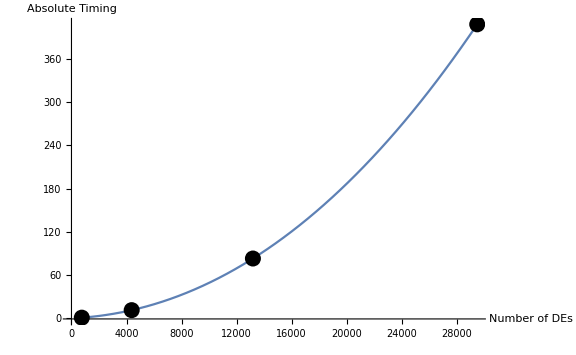

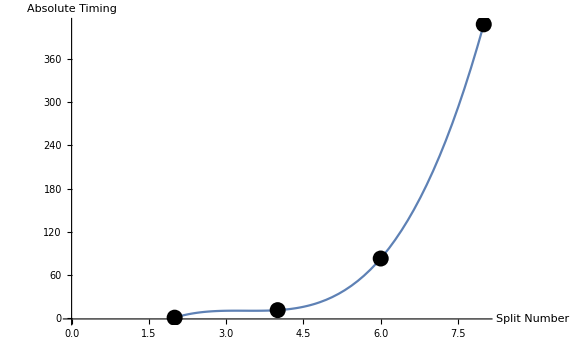

```mathematica
maxValue=8;
timeArray=AbsoluteTimingArray[maxValue];
splitNumberArray=Table[t,{t,2,maxValue,2}];
DEnumberArray=Table[(splitNumberArray[[i]]*2+1)^3*6,{i,1,Length[splitNumberArray]}];
DEnumberArrayAlternative=Table[splitNumberArray[[i]],{i,1,Length[splitNumberArray]}];
deTimeArray=Table[{DEnumberArray[[i]],timeArray[[i]]},{i,1,Length[DEnumberArray]}];
deTimeArrayAlternative=Table[{DEnumberArrayAlternative[[i]],timeArray[[i]]},{i,1,Length[DEnumberArrayAlternative]}];
Plot[Quiet[Interpolation[deTimeArray]][x],{x,DEnumberArray[[1]],DEnumberArray[[-1]]},Epilog->{PointSize[0.02],Point@deTimeArray},AxesLabel->{"Number of DEs","Absolute Timing"},AxesOrigin->{0,-1},ImageSize->Large]
Plot[Quiet[Interpolation[deTimeArrayAlternative]][x],{x,DEnumberArrayAlternative[[1]],DEnumberArrayAlternative[[-1]]},Epilog->{PointSize[0.02],Point@deTimeArrayAlternative},AxesLabel->{"Split Number","Absolute Timing"},AxesOrigin->{0,-1},ImageSize->Large]
```

```mathematica
expression=c0*Exp[c1*x];
model=NonlinearModelFit[deTimeArrayAlternative,expression,{c0,c1},x];
bestExpression=expression/.model["BestFitParameters"];
TableForm[Table[{i,bestExpression/.x->i,(bestExpression/.x->i)/3600,(bestExpression/.x->i)/(3600*24),(2 i+1)^3*6},{i,2,100,2}],TableHeadings->{None,{"Split number","Absolute time in seconds","Absolute time in hours","Absolute time in days","Number of DEs"}}]
```

Split number | Absolute time in seconds | Absolute time in hours | Absolute time in days | Number of DEs
2 | 3.15636 | 0.000876766 | 0.0000365319 | 750
4 | 15.9636 | 0.00443432 | 0.000184764 | 4374
6 | 80.7372 | 0.022427 | 0.000934459 | 13182
8 | 408.336 | 0.113427 | 0.00472611 | 29478
10 | 2065.2 | 0.573666 | 0.0239027 | 55566
12 | 10444.9 | 2.90137 | 0.12089 | 93750
14 | 52826.2 | 14.6739 | 0.611414 | 146334
16 | 267173. | 74.2148 | 3.09228 | 215622
18 | 1.35125×10^6 | 375.348 | 15.6395 | 303918
20 | 6.83409×10^6 | 1898.36 | 79.0983 | 413526
22 | 3.4564×10^7 | 9601.12 | 400.047 | 546750
24 | 1.74811×10^8 | 48558.6 | 2023.27 | 705894
26 | 8.84122×10^8 | 245589. | 10232.9 | 893262
28 | 4.47153×10^9 | 1.24209×10^6 | 51753.8 | 1111158
30 | 2.26152×10^10 | 6.28199×10^6 | 261750. | 1361886
32 | 1.14378×10^11 | 3.17718×10^7 | 1.32382×10^6 | 1647750
34 | 5.78479×10^11 | 1.60689×10^8 | 6.69536×10^6 | 1971054
36 | 2.92571×10^12 | 8.12698×10^8 | 3.38624×10^7 | 2334102
38 | 1.47971×10^13 | 4.11029×10^9 | 1.71262×10^8 | 2739198
40 | 7.48375×10^13 | 2.07882×10^10 | 8.66175×10^8 | 3188646
42 | 3.78497×10^14 | 1.05138×10^11 | 4.38076×10^9 | 3684750
44 | 1.91429×10^15 | 5.31746×10^11 | 2.21561×10^10 | 4229814
46 | 9.68168×10^15 | 2.68936×10^12 | 1.12056×10^11 | 4826142
48 | 4.8966×10^16 | 1.36017×10^13 | 5.66736×10^11 | 5476038
50 | 2.4765×10^17 | 6.87917×10^13 | 2.86632×10^12 | 6181806
52 | 1.25251×10^18 | 3.4792×10^14 | 1.44967×10^13 | 6945750
54 | 6.3347×10^18 | 1.75964×10^15 | 7.33183×10^13 | 7770174
56 | 3.20383×10^19 | 8.89954×10^15 | 3.70814×10^14 | 8657382
58 | 1.62037×10^20 | 4.50102×10^16 | 1.87543×10^15 | 9609678
60 | 8.19516×10^20 | 2.27643×10^17 | 9.48514×10^15 | 10629366
62 | 4.14478×10^21 | 1.15133×10^18 | 4.7972×10^16 | 11718750
64 | 2.09626×10^22 | 5.82295×10^18 | 2.42623×10^17 | 12880134
66 | 1.0602×10^23 | 2.94501×10^19 | 1.22709×10^18 | 14115822
68 | 5.36208×10^23 | 1.48947×10^20 | 6.20611×10^18 | 15428118
70 | 2.71192×10^24 | 7.53311×10^20 | 3.1388×10^19 | 16819326
72 | 1.37158×10^25 | 3.80994×10^21 | 1.58748×10^20 | 18291750
74 | 6.93689×10^25 | 1.92691×10^22 | 8.0288×10^20 | 19847694
76 | 3.50839×10^26 | 9.74554×10^22 | 4.06064×10^21 | 21489462
78 | 1.7744×10^27 | 4.9289×10^23 | 2.05371×10^22 | 23219358
80 | 8.97421×10^27 | 2.49283×10^24 | 1.03868×10^23 | 25039686
82 | 4.53879×10^28 | 1.26077×10^25 | 5.25323×10^23 | 26952750
84 | 2.29553×10^29 | 6.37648×10^25 | 2.65687×10^24 | 28960854
86 | 1.16099×10^30 | 3.22497×10^26 | 1.34374×10^25 | 31066302
88 | 5.8718×10^30 | 1.63106×10^27 | 6.79607×10^25 | 33271398
90 | 2.96972×10^31 | 8.24922×10^27 | 3.43717×10^26 | 35578446
92 | 1.50196×10^32 | 4.17212×10^28 | 1.73838×10^27 | 37989750
94 | 7.59631×10^32 | 2.11009×10^29 | 8.79203×10^27 | 40507614
96 | 3.84191×10^33 | 1.0672×10^30 | 4.44665×10^28 | 43134342
98 | 1.94308×10^34 | 5.39744×10^30 | 2.24893×10^29 | 45872238
100 | 9.82731×10^34 | 2.72981×10^31 | 1.13742×10^30 | 48723606